```mathematica
This is the Mathematica notebook Curvature and the Einstein Equation available from the book website.  From a given metric Subscript[g, αβ] , it computes the components of the following: the inverse metric, g^λσ, the Christoffel symbols or affine connection,
	Subscript[Γ^λ, μν]=1/2 g^λσ(D[Subscript[g, σν], μ]+D[Subscript[g, σμ], ν]-D[Subscript[g, μν], σ]),
 ( ∂_α stands for the partial derivative ∂/∂x^α), the Riemann tensor,
		Subscript[R^λ, μνσ]=D[Subscript[Γ^λ, μσ], ν]-D[Subscript[Γ^λ, μν], σ]+Subscript[Γ^η, μσ] Subscript[Γ^λ, ην]-Subscript[Γ^η, μν] Subscript[Γ^λ, ησ],
the Ricci tensor
		Subscript[R, μν]=Subscript[R^λ, μλν],
the scalar curvature,
		R=g^μν Subscript[R, μν],
and the Einstein tensor,
 	Subscript[G, μν]=Subscript[R, μν]-1/2 Subscript[g, μν] R.
```

```mathematica
Defining a list of coordinates:
```

```mathematica
coord = {t,r,θ,ϕ}
n=Length[coord]
```

{t,r,θ,ϕ}

4

```mathematica
Defining the metric:
```

```mathematica
metric={{1,0,0,0},{0,-a[t]^2/(1-K r^2),0,0},{0,0,-a[t]^2r^2,0},{0,0,0,-a[t]^2r^2Sin[θ]^2}};
metric//MatrixForm
```

(1 | 0 | 0 | 0
0 | -a[t]^2/(1-K r^2) | 0 | 0
0 | 0 | -r^2 a[t]^2 | 0
0 | 0 | 0 | -r^2 a[t]^2 Sin[θ]^2)

```mathematica
inversemetric=Simplify[Inverse[metric]];
inversemetric//MatrixForm
```

(1 | 0 | 0 | 0
0 | (-1+K r^2)/a[t]^2 | 0 | 0
0 | 0 | -1/(r^2 a[t]^2) | 0
0 | 0 | 0 | -Csc[θ]^2/(r^2 a[t]^2))

```mathematica
Calculating the Christoffel symbols:
```

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coord[[k]] ]+
D[metric[[s,k]],coord[[j]] ]-D[metric[[j,k]],coord[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 2] | (a[t] a'[t])/(1-K r^2)
Γ[1, 3, 3] | r^2 a[t] a'[t]
Γ[1, 4, 4] | r^2 a[t] Sin[θ]^2 a'[t]
Γ[2, 2, 1] | a'[t]/a[t]
Γ[2, 2, 2] | (K r)/(1-K r^2)
Γ[2, 3, 3] | r (-1+K r^2)
Γ[2, 4, 4] | r (-1+K r^2) Sin[θ]^2
Γ[3, 3, 1] | a'[t]/a[t]
Γ[3, 3, 2] | 1/r
Γ[3, 4, 4] | -Cos[θ] Sin[θ]
Γ[4, 4, 1] | a'[t]/a[t]
Γ[4, 4, 2] | 1/r
Γ[4, 4, 3] | Cot[θ]

```mathematica
Calculating the Riemann tensor:
```

```mathematica
riemann:=riemann=Simplify[Table[
D[affine[[i,j,l]],coord[[k]] ]-D[affine[[i,j,k]],coord[[l]] ]+
Sum[affine[[s,j,l]] affine[[i,k,s]]-affine[[s,j,k]] affine[[i,l,s]],
{s,1,n}],
{i,1,n},{j,1,n},{k,1,n},{l,1,n}] ]
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}] ,{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | (a[t] a''[t])/(-1+K r^2)
R[1, 3, 3, 1] | -r^2 a[t] a''[t]
R[1, 4, 4, 1] | -r^2 a[t] Sin[θ]^2 a''[t]
R[2, 1, 2, 1] | -a''[t]/a[t]
R[2, 3, 3, 2] | -r^2 (K+a'[t]^2)
R[2, 4, 4, 2] | -r^2 Sin[θ]^2 (K+a'[t]^2)
R[3, 1, 3, 1] | -a''[t]/a[t]
R[3, 2, 3, 2] | (K+a'[t]^2)/(1-K r^2)
R[3, 4, 4, 3] | -r^2 Sin[θ]^2 (K+a'[t]^2)
R[4, 1, 4, 1] | -a''[t]/a[t]
R[4, 2, 4, 2] | (K+a'[t]^2)/(1-K r^2)
R[4, 3, 4, 3] | r^2 (K+a'[t]^2)

```mathematica
Calculating the Ricci tensor:
```

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}] ]
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}] ,{j,1,n},{l,1,j}]
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | -(3 a''[t])/a[t]
R[2, 2] | (2 K+2 a'[t]^2+a[t] a''[t])/(1-K r^2)
R[3, 3] | r^2 (2 (K+a'[t]^2)+a[t] a''[t])
R[4, 4] | r^2 Sin[θ]^2 (2 (K+a'[t]^2)+a[t] a''[t])

```mathematica
Calculating the curvature scalar:
```

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}] ]
scalar//Factor
```

-(6 (K+a'[t]^2+a[t] a''[t]))/a[t]^2

-(6 (K+a'[t]^2+a[t] a''[t]))/a[t]^2

```mathematica
Calculating the Einstein tensor including cosmological constant:
```

```mathematica
einstein:=einstein=Simplify[ricci-(1/2)scalar metric+Λ metric]
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}] ,{j,1,n},{l,1,j}]
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

G[1, 1] | Λ+(3 (K+a'[t]^2))/a[t]^2
G[2, 2] | (K+Λ a[t]^2+a'[t]^2+2 a[t] a''[t])/(-1+K r^2)
G[3, 3] | -r^2 (K+Λ a[t]^2+a'[t]^2+2 a[t] a''[t])
G[4, 4] | -r^2 Sin[θ]^2 (K+Λ a[t]^2+a'[t]^2+2 a[t] a''[t])

```mathematica
Energy momentum tensor for a fluid:
```

```mathematica
Clear[energyMomentum]
u={1,0,0,0};
energyMomentum:=energyMomentum=(ρ[t]+P[t])TensorProduct[u,u]-P[t] metric

listenergyMomentum:=Table[If[UnsameQ[energyMomentum[[j,l]],0],{ToString[T[j,l]],energyMomentum[[j,l]]}] ,{j,1,n},{l,1,j}]

TableForm[Partition[DeleteCases[Flatten[listenergyMomentum],Null],2],TableSpacing->{2,2}]
```

T[1, 1] | ρ[t]
T[2, 2] | (a[t]^2 P[t])/(1-K r^2)
T[3, 3] | r^2 a[t]^2 P[t]
T[4, 4] | r^2 a[t]^2 P[t] Sin[θ]^2

```mathematica
Friedmann equations:
```

```mathematica
friedmann1 = einstein[[1,1]]-8Pi energyMomentum[[1,1]]//Simplify//Expand;
friedmann1==0
friedmann2a=einstein[[2,2]]-8Pi energyMomentum[[2,2]]//Simplify//Expand;
friedmann2b=friedman2a(-1+K r^2)-friedmann1 a[t]^2/3//Simplify//Expand;
friedmann2=friedmann2b/(2 a[t]^2)//Simplify//Expand;
friedmann2==0
```

Λ+(3 K)/a[t]^2-8 π ρ[t]+(3 a'[t]^2)/a[t]^2==0

Λ/3+4 π P[t]+4/3 π ρ[t]+a''[t]/a[t]==0

```mathematica
Continuity equation from Friedmann equations:
```

```mathematica
D[friedmann1 a[t]^2,t]-friedmann2 a[t] 6 a'[t] //Expand;
continuity=%/(-8 Pi a[t]^2)//Expand;
continuity==0
```

(3 P[t] a'[t])/a[t]+(3 ρ[t] a'[t])/a[t]+ρ'[t]==0

```mathematica
Dust (P=0):
```

```mathematica
continuity//.P[t]->0//.{ρ[t]->ρM[t],ρ'[t]->ρM'[t]};
ruleM=DSolve[{%==0,ρM[t0]==ρM0},ρM[t],t][[1,1]]
```

ρM[t]→(ρM0 a[t0]^3)/a[t]^3

```mathematica
Radiation (P=ρ/3):
```

```mathematica
continuity//.P[t]->ρR[t]/3//.{ρ[t]->ρR[t],ρ'[t]->ρR'[t]};
ruleR=DSolve[{%==0,ρR[t0]==ρR0},ρR[t],t][[1,1]]
```

ρR[t]→(ρR0 a[t0]^4)/a[t]^4

```mathematica
Define more energy densities:
```

```mathematica
ruleΛ=Λ->-8π ρΛ0
rulek=K->-(8π)/3 ρk0 a[t0]^2
ruleΩ={ρcrit->3/(8π)H0^2,ρM0->ΩM ρcrit,ρR0->ΩR ρcrit,ρΛ0->ΩΛ ρcrit,ρk0->Ωk ρcrit}
```

Λ→-8 π ρΛ0

K→-8/3 π ρk0 a[t0]^2

{ρcrit→(3 H0^2)/(8 π),ρM0→ρcrit ΩM,ρR0→ρcrit ΩR,ρΛ0→ρcrit ΩΛ,ρk0→ρcrit Ωk}

```mathematica
1/3 friedmann1==0//.ρ[t]->ρM[t]+ρR[t]//.ruleM//.ruleR//.ruleΛ//.rulek//Expand
%//.ruleΩ
```

-(8 π ρΛ0)/3-(8 π ρk0 a[t0]^2)/(3 a[t]^2)-(8 π ρM0 a[t0]^3)/(3 a[t]^3)-(8 π ρR0 a[t0]^4)/(3 a[t]^4)+a'[t]^2/a[t]^2==0

-H0^2 ΩΛ-(H0^2 Ωk a[t0]^2)/a[t]^2-(H0^2 ΩM a[t0]^3)/a[t]^3-(H0^2 ΩR a[t0]^4)/a[t]^4+a'[t]^2/a[t]^2==0

```mathematica
HubbleNow=1.0;
rule1={ΩM->0.99,ΩR->0.0001,Ωk->-k/(a0^2 H0^2),ΩΛ->1-ΩM-ΩR-Ωk,k->-1,t0->0,a0->1,H0->HubbleNow};
s1=NDSolve[{a'[t]==H0 √(ΩΛ a[t]^2+Ωk a[t0]^2+(ΩM a[t0]^3)/a[t]+(ΩR a[t0]^4)/a[t]^2)//.a[t0]->1,a[t0]==a0}//.rule1,a[t],{t,-2,5}];
rule2={ΩM->0.3,ΩR->0.0001,Ωk->-k/(a0^2 H0^2),ΩΛ->1-ΩM-ΩR-Ωk,k->0,t0->0,a0->1,H0->HubbleNow};
s2=NDSolve[{a'[t]==H0 √(ΩΛ a[t]^2+Ωk a[t0]^2+(ΩM a[t0]^3)/a[t]+(ΩR a[t0]^4)/a[t]^2)//.a[t0]->1,a[t0]==a0}//.rule2,a[t],{t,-2,5}];
rule3={ΩM->5,ΩR->0.0001,Ωk->-k/(a0^2 H0^2),ΩΛ->1-ΩM-ΩR-Ωk,k->1,t0->0,a0->1,H0->HubbleNow};
s3=NDSolve[{a'[t]==H0 √(ΩΛ a[t]^2+Ωk a[t0]^2+(ΩM a[t0]^3)/a[t]+(ΩR a[t0]^4)/a[t]^2)//.a[t0]->1,a[t0]==a0}//.rule3,a[t],{t,-2,5}];
rule4={ΩM->1,ΩR->0.0001,Ωk->-k/(a0^2 H0^2),ΩΛ->1-ΩM-ΩR-Ωk,k->1,t0->0,a0->1,H0->HubbleNow};
s4=NDSolve[{a'[t]==H0 √(ΩΛ a[t]^2+Ωk a[t0]^2+(ΩM a[t0]^3)/a[t]+(ΩR a[t0]^4)/a[t]^2)//.a[t0]->1,a[t0]==a0}//.rule4,a[t],{t,-2,5}];
```

NDSolve::ndsz: At t == -0.595595, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 137772 steps reached at the point t == 0.646888.

NDSolve::mxst: Maximum number of 137772 steps reached at the point t == -0.963672.

NDSolve::ndcf: Repeated convergence test failure at t == -0.383419; unable to continue.

NDSolve::mxst: Maximum number of 137772 steps reached at the point t == 0.185403.

NDSolve::mxst: Maximum number of 137772 steps reached at the point t == -0.784494.

InterpolatingFunction::dmval: Input value {-0.999939} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.99,-0.9901,0.0001,1.}

InterpolatingFunction::dmval: Input value {-0.999939} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.3,0.6999,0.0001,0.}

InterpolatingFunction::dmval: Input value {-0.499949} lies outside the range of data in the interpolating function. Extrapolation will be used.

{5,-3.0001,0.0001,-1.}

InterpolatingFunction::dmval: Input value {-0.999939} lies outside the range of data in the interpolating function. Extrapolation will be used.

{1,0.9999,0.0001,-1.}

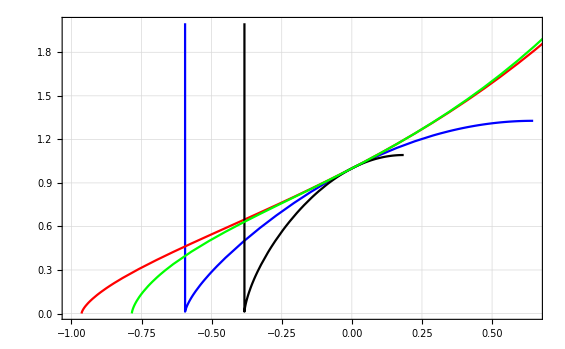

```mathematica
p1=Plot[Evaluate[a[t]/.s1],{t,-1,2},PlotStyle->{Blue},PlotRange->{0,2},Frame->True,GridLines->Automatic];
{ΩM,ΩΛ,ΩR,Ωk}//.rule1
p2=Plot[Evaluate[a[t]/.s2],{t,-1,2},PlotStyle->{Red},PlotRange->{0,2},Frame->True,GridLines->Automatic];
{ΩM,ΩΛ,ΩR,Ωk}//.rule2
p3=Plot[Evaluate[a[t]/.s3],{t,-0.5,2},PlotStyle->{Black},PlotRange->{0,2},Frame->True,GridLines->Automatic];
{ΩM,ΩΛ,ΩR,Ωk}//.rule3
p4=Plot[Evaluate[a[t]/.s4],{t,-1,2},PlotStyle->{Green},PlotRange->{0,2},Frame->True,GridLines->Automatic];
{ΩM,ΩΛ,ΩR,Ωk}//.rule4
Show[{p1,p2,p3,p4}]
```